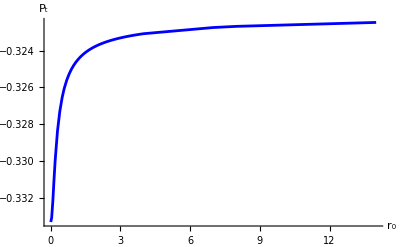

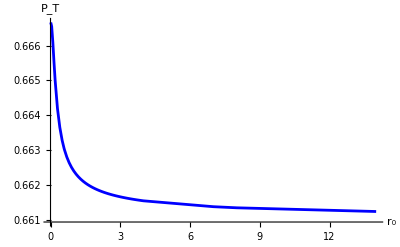

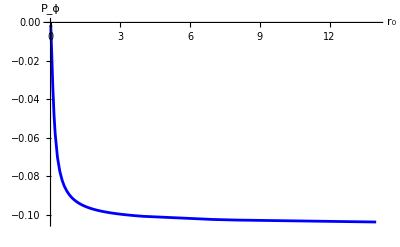

```mathematica
PtPlot=ListPlot[Table[{Con1[[i,1]],Con1[[i,6]]},{i,1,Length[Con1]}], PlotRange->All,PlotStyle->Blue,AxesLabel->{Style[" r_0",FontSize->18],Style["P_t", FontSize->18]},Joined->True]
PTPlot=ListPlot[Table[{Con1[[i,1]],Con1[[i,7]]},{i,1,Length[Con1]}],PlotRange->All,PlotStyle->Blue,AxesLabel->{Style[" r_0",FontSize->18],Style["P_T",FontSize->18]},Joined->True]
P3Plot=ListPlot[Table[{Con1[[i,1]],Con1[[i,8]]},{i,1,Length[Con1]}],PlotRange->All,PlotStyle->Blue,AxesLabel->{Style[" r_0",FontSize->18],Style["P_ϕ", FontSize->18]},Joined->True]
Table[{Con1[[i,1]],Con1[[i,6]],Con1[[i,7]],Con1[[i,8]]},{i,34,Length[Con1]}];
PtRES=Table[{Con1[[i,6]]},{i,34,Length[Con1]}]
```